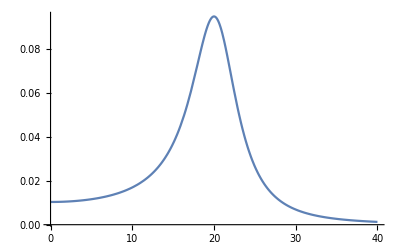

```mathematica
m := 20
Γ := 7
k := (2 Sqrt[2] m Γ γ/(Pi Sqrt[m^2 + γ]))
γ  := Sqrt[m^2(m^2 + Γ^2)]
σ[e_] := (k/((e^2 -m^2)^2 + m^2 Γ^2))
Plot[σ[e],{e,0,40},PlotRange->All]
```

```mathematica
Clear[m,Γ,k,γ]
γ[m_,Γ_]  := Sqrt[m^2(m^2 + Γ^2)]
k[m_,Γ_] := (2 Sqrt[2] m Γ γ[m,Γ]/(Pi Sqrt[m^2 + γ[m,Γ]]))
σ2[e_,m_,Γ_] := (k[m,Γ]/((e^2 -m^2)^2 + m^2 Γ^2))
Manipulate[Plot[σ2[e,m,Γ],{e,0,100},PlotRange->Full],{m,0.001,100},{Γ,0.001,100}]
```

```mathematica
Clear[e,m,Γ,k,γ]
(*k := (2 Sqrt[2] m Γ γ/(Pi Sqrt[m^2 + γ]))
γ  := Sqrt[m^2(m^2 + Γ^2)]*)
s :=(1/((e^2 -m^2)^2 + m^2 Γ^2))
Limit[s,e->m]//Simplify
Limit[s,e->(m+(Γ/2))]//Simplify
Limit[s,e->(m-(Γ/2))]//Simplify
Limit[s,e->(m+(1/(m^2 Γ^2)))]//Simplify
Limit[s,e->(m-(1/(m^2 Γ^2)))]//Simplify
```

1/(m^2 Γ^2)

16/(Γ^2 (32 m^2+8 m Γ+Γ^2))

16/(Γ^2 (32 m^2-8 m Γ+Γ^2))

(m^8 Γ^8)/(1+4 m^3 Γ^2+4 m^6 Γ^4+m^10 Γ^10)

(m^8 Γ^8)/(1-4 m^3 Γ^2+4 m^6 Γ^4+m^10 Γ^10)